2.)

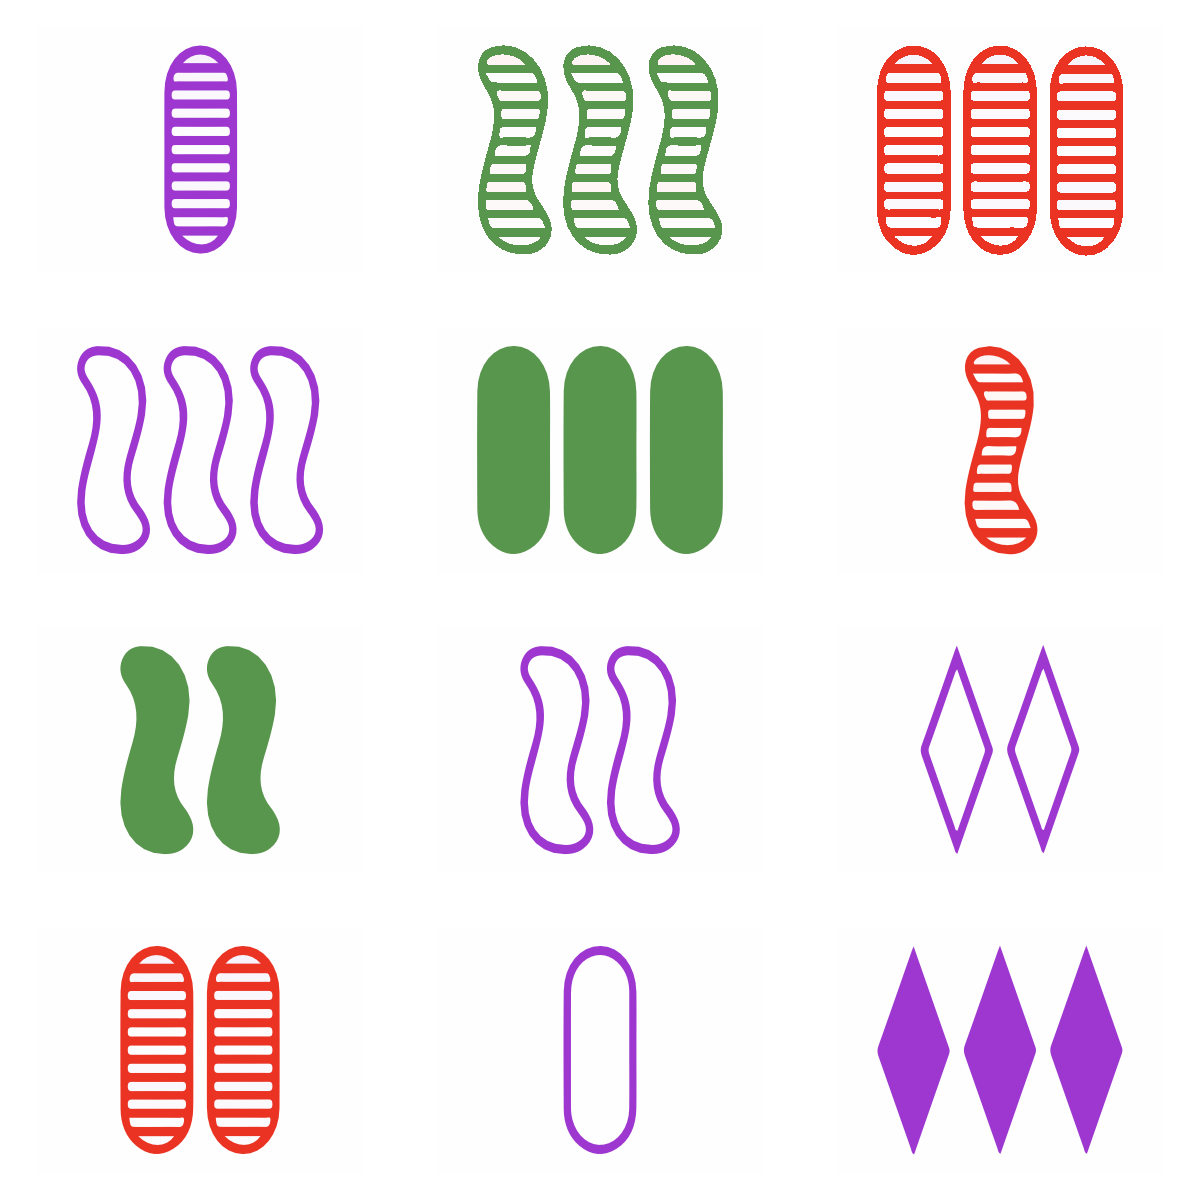

{{{1,RGBColor[0.5, 0, 0.5],striped,oval},{2,RGBColor[0.5, 0, 0.5],empty,squiggle},{3,RGBColor[0.5, 0, 0.5],solid,diamond}},{{3,RGBColor[0.5, 0, 0.5],empty,squiggle},{1,RGBColor[1, 0, 0],striped,squiggle},{2,RGBColor[0, 1, 0],solid,squiggle}},{{3,RGBColor[0.5, 0, 0.5],empty,squiggle},{2,RGBColor[0.5, 0, 0.5],empty,diamond},{1,RGBColor[0.5, 0, 0.5],empty,oval}},{{3,RGBColor[0, 1, 0],solid,oval},{1,RGBColor[1, 0, 0],striped,squiggle},{2,RGBColor[0.5, 0, 0.5],empty,diamond}},{{3,RGBColor[0, 1, 0],solid,oval},{2,RGBColor[1, 0, 0],striped,oval},{1,RGBColor[0.5, 0, 0.5],empty,oval}},{{2,RGBColor[0, 1, 0],solid,squiggle},{2,RGBColor[0.5, 0, 0.5],empty,diamond},{2,RGBColor[1, 0, 0],striped,oval}}}

```mathematica
cards = Select[
Table[RandomSample[setDeck,12],2000],
Length[Select[Map[setCheck[#]&,Subsets[#,{3}]],#==True&]]==6&
][[1]];

setToImage/@Partition[
cards,
3
]//TableForm

Select[
Subsets[cards,{3}],
setCheck[#]==True&
]
```

3.)

```mathematica
TableForm[
Table[
{
x,
3^x,
(3^x ((3^x)-1))/(3!),
(3^x ((3^x)-1)((3^x)-3))/(3!)/72
},
{x,3,20}
],
TableAlignments->Center,
TableHeadings->{None,{"attributes","cards","sets","planes"}},
TableSpacing->{1,3}
]
```

attributes | cards | sets | planes
3 | 27 | 117 | 39
4 | 81 | 1080 | 1170
5 | 243 | 9801 | 32670
6 | 729 | 88452 | 891891
7 | 2187 | 796797 | 24169509
8 | 6561 | 7173360 | 653373540
9 | 19683 | 64566801 | 17648258940
10 | 59049 | 581120892 | 476567558181
11 | 177147 | 5230147077 | 12867905191779
12 | 531441 | 47071500840 | 347438670325110
13 | 1594323 | 423644039001 | 9380891170278810
14 | 4782969 | 3812797945332 | 253284485241566871
15 | 14348907 | 34315186290957 | 6838684914320250849
16 | 43046721 | 308836690967520 | 184644527001833063880
17 | 129140163 | 2779530261754401 | 4985402537886183692280
18 | 387420489 | 25015772484929772 | 134605871302457221445961
19 | 1162261467 | 225141952751788437 | 3634358550182117463970719
20 | 3486784401 | 2026277575928357400 | 98127681080059124278997850